```mathematica
(* first let's define a complicated function *)
```

```mathematica
f[x_]=E^(-x^2+x)
```

ⅇ^(x-x^2)

```mathematica
(* now let's compute the coefficients using numerical integration and store the coefficients in a[k] for Legendre polynomial expansion *)
```

```mathematica
For[k=0,k<30,k++,
a[k]=NIntegrate[f[x]*LegendreP[k,x],{x,-1,1},WorkingPrecision->40,PrecisionGoal->20,MaxRecursion->12]/NIntegrate[LegendreP[k,x]^2,{x,-1,1},WorkingPrecision->40,PrecisionGoal->20,MaxRecursion->12];Print[a[k]]]
```

0.845832097678374092578166925346523553251

0.620249608945020657787750009249148632432

-0.296151522789405359343852884828818024286

-0.214158873327153087340510354620294590769

0.0172276727791163117437273031938466203524

0.0283866725921421678777117031181972915427

0.00096577053759906266628013140373078743844

-0.00226699380612820853712184515743701408776

-0.000224618422815533532005153671208994357281

0.00012715294096594916263458221885604545218

0.000019308805807968151472985575945015370162

-5.38217665933839376203919954207774080113×10^-6

-1.11471968336233095492316701392814266178×10^-6

1.77708827401741814861483460621197019819×10^-7

4.94924798524758125621754568696644619089×10^-8

-4.58161525284717800729589320100082631991×10^-9

-1.79702021946995296377569000648827705292×10^-9

8.71994549349677670618667458571965695198×10^-11

5.52956544266410730303061228491496773857×10^-11

-8.92762520818585521981183160716247638021×10^-13

-1.47616274852484515801698221204676931188×10^-12

-1.44035349461931044351766247070797647704×10^-14

3.47583936525967414973454799028925005761×10^-14

1.11306616056379937944952363712303445791×10^-15

-7.30665006829166035326292418026248701791×10^-16

-3.83234582192446737427180410327892404442×10^-17

1.38353922390511898614739078674341908956×10^-17

1.00143012036969543008800865421031417727×10^-18

-2.37508257196235269882617163926612395422×10^-19

-2.20964066760824195533129683195229335705×10^-20

```mathematica
(* Now let's check the error for different terms *)
```

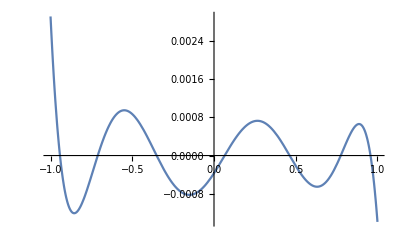

```mathematica
Plot[f[x]-Sum[a[k]*LegendreP[k,x],{k,0,5}],{x,-1,1}]
```

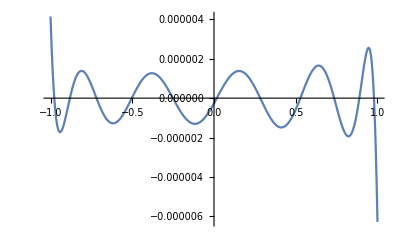

```mathematica
Plot[f[x]-Sum[a[k]*LegendreP[k,x],{k,0,10}],{x,-1,1}]
```

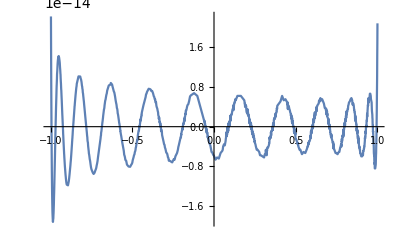

```mathematica
Plot[f[x]-Sum[a[k]*LegendreP[k,x],{k,0,20}],{x,-1,1}]
```